```mathematica
b = 0.3
F0 = 0.5
w = 3
P = NDSolve[{x''[t] + Sign[x'[t]]*b*(x'[t])^2 + x[t] == F0*Cos[w*t], x[0]==1, x'[0]==0}, x, {t,0,1000}];
```

0.3

0.5

3

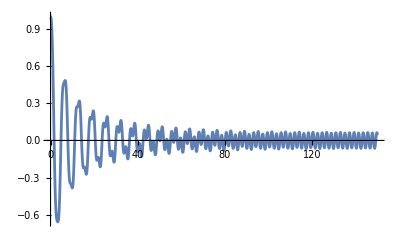

```mathematica
Plot[Evaluate[x[t]/.P], {t,0,150}, PlotRange->All]
```

1

0.5

0.5

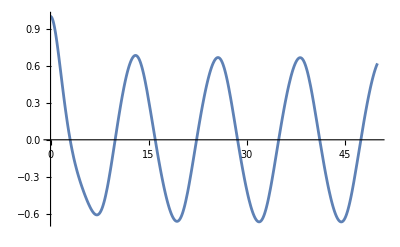

NMaximize[{InterpolatingFunction[…][t]},t∈{950,990}]

1

0.5

ReplaceAll::reps: {} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

```mathematica
b = 1
F0 = 0.5
w = 0.5
P = NDSolve[{x''[t] + Sign[x'[t]]*b*(x'[t])^2 + x[t] == F0*Cos[w*t], x[0]==1, x'[0]==0}, x, {t,0,1000}];
Plot[Evaluate[x[t]/.P], {t,0, 50}, PlotRange->All]
NMaximize[x[t]/.P,t ∈{950,990}]
```

```mathematica
3
```

3

1

0.5

2.9

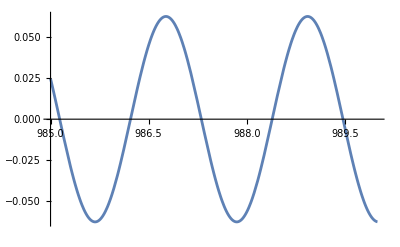

```mathematica
b = 1
F0 = 0.5
w = 2.9
P = NDSolve[{x''[t] + b*(x'[t]) + x[t] == F0*Cos[w*t], x[0]==1, x'[0]==0}, x, {t,0,1000}];
Plot[Evaluate[x[t]/.P], {t,985, 990}, PlotRange->All]
```

```mathematica
[]
```

```mathematica
(Cos[t1/2] P - ⅈ s2 Sin[t1/2])(Cos[t2/2] P- ⅈ s3 Sin[t2/2])
```

(P Cos[t1/2]-ⅈ s2 Sin[t1/2]) (P Cos[t2/2]-ⅈ s3 Sin[t2/2])

```mathematica
Expand[%]
```

```mathematica
Cos[t1/2] Cos[t2/2]-ⅈ s2 Cos[t2/2] Sin[t1/2]-ⅈ s3 Cos[t1/2] Sin[t2/2]- ⅈ s1 Sin[t1/2] Sin[t2/2]
```

```mathematica
Cos[t1/2] Cos[t2/2]-ⅈ s2 Cos[t2/2] Sin[t1/2]-ⅈ s3 Cos[t1/2] Sin[t2/2]-ⅈ s1 Sin[t1/2] Sin[t2/2]
```

Cos[t1/2] Cos[t2/2]-ⅈ s2 Cos[t2/2] Sin[t1/2]-ⅈ s3 Cos[t1/2] Sin[t2/2]-ⅈ s1 Sin[t1/2] Sin[t2/2]

```mathematica
TrigReduce[Cos[t1/2] Cos[t2/2]-ⅈ s2 Cos[t2/2] Sin[t1/2]-ⅈ s3 Cos[t1/2] Sin[t2/2]-ⅈ s1 Sin[t1/2] Sin[t2/2]]
```

-1/2 ⅈ (ⅈ Cos[t1/2-t2/2]+s1 Cos[t1/2-t2/2]+ⅈ Cos[t1/2+t2/2]-s1 Cos[t1/2+t2/2]+s2 Sin[t1/2-t2/2]-s3 Sin[t1/2-t2/2]+s2 Sin[t1/2+t2/2]+s3 Sin[t1/2+t2/2])

```mathematica
Simplify[-1/2 ⅈ (ⅈ Cos[t1/2-t2/2]+s1 Cos[t1/2-t2/2]+ⅈ Cos[t1/2+t2/2]-s1 Cos[t1/2+t2/2]+s2 Sin[t1/2-t2/2]-s3 Sin[t1/2-t2/2]+s2 Sin[t1/2+t2/2]+s3 Sin[t1/2+t2/2])]
```

-ⅈ Sin[t1/2] (s2 Cos[t2/2]+s1 Sin[t2/2])+Cos[t1/2] (Cos[t2/2]-ⅈ s3 Sin[t2/2])

```mathematica
TrigReduce[-ⅈ Sin[t1/2] (s2 Cos[t2/2]+s1 Sin[t2/2])+Cos[t1/2] (Cos[t2/2]-ⅈ s3 Sin[t2/2])]
```

-1/2 ⅈ (ⅈ Cos[t1/2-t2/2]+s1 Cos[t1/2-t2/2]+ⅈ Cos[t1/2+t2/2]-s1 Cos[t1/2+t2/2]+s2 Sin[t1/2-t2/2]-s3 Sin[t1/2-t2/2]+s2 Sin[t1/2+t2/2]+s3 Sin[t1/2+t2/2])

```mathematica
Expand[%]
```

1/2 Cos[t1/2-t2/2]-1/2 ⅈ s1 Cos[t1/2-t2/2]+1/2 Cos[t1/2+t2/2]+1/2 ⅈ s1 Cos[t1/2+t2/2]-1/2 ⅈ s2 Sin[t1/2-t2/2]+1/2 ⅈ s3 Sin[t1/2-t2/2]-1/2 ⅈ s2 Sin[t1/2+t2/2]-1/2 ⅈ s3 Sin[t1/2+t2/2]